```mathematica
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"];
```

```mathematica
SetDirectory["~/Desktop/Modeling/Data"]
```

/home/adam/Desktop/Modeling/Data

```mathematica
Datastuff= Import["ProblemC56Var.xlsx"];
```

```mathematica
Clear[f]
f[{x_,y_,z_,a_}]:={x,y,IntegerPart[z],a}
```

```mathematica
Clear[ModifiedData]
ModifiedData=Map[f,Datastuff[[1]]];
```

```mathematica
Clear[AZData,TXData,NMData,CAData]
AZData=Cases[ModifiedData,{_,"AZ",_,_}];
TXData=Cases[ModifiedData,{_,"TX",_,_}];
NMData=Cases[ModifiedData,{_,"NM",_,_}];
CAData=Cases[ModifiedData,{_,"CA",_,_}];
```

```mathematica
StateData={AZData,TXData,NMData,CAData};
```

```mathematica
Produced=Drop[Map[First,Datastuff[[2]]],2];
```

```mathematica
Consumed=Flatten@Drop[Drop[Map[Take[#,{4}]&,Datastuff[[2]]],2],-34];
```

```mathematica
Clear[TimeFunc,VarFunc,RemoveState,ProducedVars,ConsumedVars,DataFunc]
VarFunc[{a_,b_,c_,d_}]:={a}
TimeFunc[{a_,b_,c_,d_}]:={c,d}
RemoveState[{a_,b_,c_,d_}]:={a,c,d}
DataFunc[{a_,b_,c_,d_}]:=d
ProducedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Produced}]]
ConsumedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Consumed}]]
```

```mathematica
Clear[AZProduced,TXProduced,NMProduced,CAProduced]
{AZProduced,TXProduced,NMProduced,CAProduced}=Map[ProducedVars,StateData];
```

```mathematica
Clear[AZConsumed,TXConsumed,NMConsumed,CAConsumed]
{AZConsumed,TXConsumed,NMConsumed,CAConsumed}=Map[ConsumedVars,StateData];
```

```mathematica
Clear[TimeRemove]
TimeRemove[dataset_]:=Map[TimeFunc[#]&,dataset]
```

```mathematica
Clear[LastModelV2];
LastModelV2[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[lists,Table[Map[Last,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[ModelV2];
ModelV2[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];
Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];
LastModelV2[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,lists,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
lists={};
lists=Append[lists,Table[Map[Last,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModelV2[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModelV2[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}]}
;n++];
Return[lists];
]
```

```mathematica
Clear[TaylorSeriesLastV2]
TaylorSeriesLastV2[x_,{n0_}]:=x*(t-49)^(n0-1)*(1/Factorial[n0])
```

```mathematica
lists=ModelV2[{AZProduced,TXProduced,NMProduced,CAProduced}];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

```mathematica
Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes]
AZSlopes=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
TXSlopes=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
NMSlopes=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
CASlopes=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_Last]&,i],{i,Drop[lists,-1]}]]]];
```

```mathematica
AZMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,AZSlopes}];
TXMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,TXSlopes}];
NMMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,NMSlopes}];
CAMonomials=Table[MapIndexed[TaylorSeriesLast,i],{i,CASlopes}];
```

```mathematica
AZSystemConsumption=Map[Total,AZMonomials];
TXSystemConsumption=Map[Total,TXMonomials];
NMSystemConsumption=Map[Total,NMMonomials];
CASystemConsumption=Map[Total,CAMonomials];
```

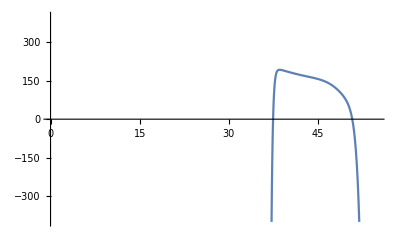

```mathematica
Plot[AZSystemConsumption[[1]],{t,30,55},PlotRange->{{0,55},{-400,400}}]
```

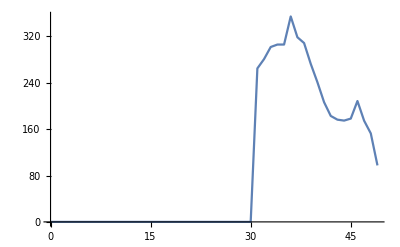

-Graphics-

```mathematica
Clear[LastModelV1];
LastModelV1[data_]:=Module[{d=data},
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[OverlappedLists,d];
{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
lists=Append[lists,Table[Map[Last,i],{i,{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}}]];
];
```

```mathematica
Clear[ModelV1];
ModelV1[dataset_]:=Module[
{data0=dataset},
Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];
Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];
LastModelV1[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}];
Clear[n,lists,PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
lists={};
lists=Append[lists,Table[Map[Last,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
LastModelV1[{AZPart,TXPart,NMPart,CAPart}];
While[
n<49,
{LastModelV1[{PyramidalSubtractionAZ,PyramidalSubtractionTX,PyramidalSubtractionNM,PyramidalSubtractionCA}]}
;n++];
Return[lists];
]
```

```mathematica
AZSystemConsumptionV1
```

{74+24 1+5.88549×10^-47 (-2+t)^47+1.94869×10^-48 (-1+t)^48+6.24123×10^-50 t^49,1,1,1,37,1,1,1,1}
 |  |  |  |

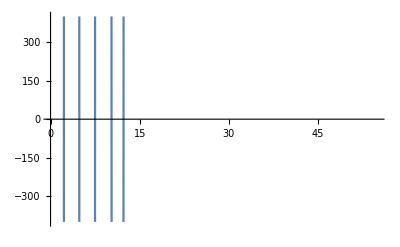

-Graphics-

```mathematica
Plot[AZSystemConsumptionV1[[1]],{t,0,55},PlotRange->{{0,55},{-400,400}}]
```

```mathematica
Clear[LastModelMedian];
LastModelMedian[data_]:=Module[{d=data},
{PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian}=Map[OverlappedLists,d];
{PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian}=Map[Table[CROC[i],{i,#}]&,{PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian}];
Medianlists=Append[Medianlists,Table[Map[Median,i],{i,{PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian}}]];
];
```

```mathematica
Clear[ModelMedian];
ModelMedian[dataset_]:=Module[
{data0=dataset},
Clear[AZPartMedian,TXPartMedian,NMPartMedian,CAPartMedian];
{AZPartMedian,TXPartMedian,NMPartMedian,CAPartMedian}=Table[Map[DataFunc[DeleteDuplicates[Chop[#]]]&,i,{2}],{i,data0}];

Clear[CalculatingROC,OverlappedLists,Pairs,CROC];
CalculatingROC[{a_,b_}]:=b-a;
CROC[data_]:=Table[CalculatingROC[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
Pairs[data_]:=Map[Partition[#,2,1]&,data];

LastModelMedian[{PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian}];
Clear[n,Medianlists,PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian];
n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];
Medianlists={};
Medianlists=Append[lists,Table[Map[Median,i],{i,{AZPartMedian,TXPartMedian,NMPartMedian,CAPartMedian}}]];
LastModelMedian[{AZPartMedian,TXPartMedian,NMPartMedian,CAPartMedian}];
While[
n<49,
{LastModelMedian[{PyramidalSubtractionAZMedian,PyramidalSubtractionTXMedian,PyramidalSubtractionNMMedian,PyramidalSubtractionCAMedian}]}
;n++];
Return[Medianlists];
]
```

```mathematica
Clear[TaylorSeriesLastMedian]
TaylorSeriesLastMedian[x_,{n0_}]:=x*(t-49)^(n0-1)*(1/Factorial[n0])
```

```mathematica
Clear[AZSlopesMedian,TXSlopesMedian,NMSlopesMedian,CASlopesMedian]
AZSlopesMedian=Transpose[PadRight[Map[Part[#,1]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[listsMedian,-1]}]]]];
TXSlopesMedian=Transpose[PadRight[Map[Part[#,2]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[listsMedian,-1]}]]]];
NMSlopesMedian=Transpose[PadRight[Map[Part[#,3]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[listsMedian,-1]}]]]];
CASlopesMedian=Transpose[PadRight[Map[Part[#,4]&,Table[Map[DeleteCases[#,_Median]&,i],{i,Drop[listsMedian,-1]}]]]];
```

```mathematica
AZMonomialsMedian=Table[MapIndexed[TaylorSeriesLastMedian,i],{i,AZSlopesMedian}];
TXMonomialsMedian=Table[MapIndexed[TaylorSeriesLastMedian,i],{i,TXSlopesMedian}];
NMMonomialsMedian=Table[MapIndexed[TaylorSeriesLastMedian,i],{i,NMSlopesMedian}];
CAMonomialsMedian=Table[MapIndexed[TaylorSeriesLastMedian,i],{i,CASlopesMedian}];
```

```mathematica
AZSystemConsumptionMedian=Map[Total,AZMonomialsMedian];
TXSystemConsumptionMedian=Map[Total,TXMonomialsMedian];
NMSystemConsumptionMedian=Map[Total,NMMonomialsMedian];
CASystemConsumptionMedian=Map[Total,CAMonomialsMedian];
```

```mathematica
AZSystemConsumptionMedian[[1]]
```

97.4778-27.6047 (-49+t)-5.55039 (-49+t)^2-1.89 (-49+t)^3-1.01405 (-49+t)^4-0.401557 (-49+t)^5-0.112984 (-49+t)^6-0.024409 (-49+t)^7-0.00424967 (-49+t)^8-0.00061189 (-49+t)^9-0.000073969 (-49+t)^10-7.60788×10^-6 (-49+t)^11-6.86298×10^-7 (-49+t)^12-6.02797×10^-8 (-49+t)^13-6.57935×10^-9 (-49+t)^14-1.02536×10^-9 (-49+t)^15-1.85483×10^-10 (-49+t)^16-3.20495×10^-11 (-49+t)^17-4.97373×10^-12 (-49+t)^18-6.87321×10^-13 (-49+t)^19-8.49001×10^-14 (-49+t)^20-9.42209×10^-15 (-49+t)^21-9.42688×10^-16 (-49+t)^22-8.50648×10^-17 (-49+t)^23-6.89403×10^-18 (-49+t)^24-4.95758×10^-19 (-49+t)^25-3.07234×10^-20 (-49+t)^26-1.51601×10^-21 (-49+t)^27-4.20007×10^-23 (-49+t)^28+2.20465×10^-24 (-49+t)^29+4.98817×10^-25 (-49+t)^30+5.40679×10^-26 (-49+t)^31+4.60645×10^-27 (-49+t)^32+3.40677×10^-28 (-49+t)^33+2.27302×10^-29 (-49+t)^34+1.39534×10^-30 (-49+t)^35+7.97415×10^-32 (-49+t)^36+4.27601×10^-33 (-49+t)^37+2.16383×10^-34 (-49+t)^38+1.03788×10^-35 (-49+t)^39+4.73524×10^-37 (-49+t)^40+2.06105×10^-38 (-49+t)^41+8.57974×10^-40 (-49+t)^42+3.42333×10^-41 (-49+t)^43+1.31175×10^-42 (-49+t)^44+4.83537×10^-44 (-49+t)^45+1.71739×10^-45 (-49+t)^46+5.88549×10^-47 (-49+t)^47+1.94869×10^-48 (-49+t)^48+6.24123×10^-50 (-49+t)^49+((-49+t)^50 Last[{}])/1551118753287382280224243016469303211063259720016986112000000000000

```mathematica
Plot[AZSystemConsumptionMedian[[1]],{t,0,50},PlotRange->{{0,70},{0,400}}]
```

-Graphics-